```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import["../a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import["../LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import["../LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

(*activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];*)
activeLEC=LECsUNITmartinrimas[[All,{1,2,3}]];
```

```mathematica
hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=3 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]

dimerCores={{2.00,{{3.49894,20.5763},{1.31002,2.03082},{0.230922,56.5742},{0.136023,20.549},{0.146917,20.5961}}}};
λRange=Range[1,Length[activeLEC]];
```

ℏ^2/(2  μ) = 13.8237

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

```mathematica
NormTF[core_?ArrayQ]:=1/Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^6/27)(1/((core[[i]][[2]]+core[[j]][[2]])(core[[k]][[2]]+core[[l]][[2]])))^6,{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_]:=Block[{eta1,eta2,eta3,w1,w2,w3},
eta2= 3^(7/2)Cc /(((Aa+Bb)(Gg+Hh)(2 lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2 lam+3Gg+3Hh)))^(3/2));
w2= 3(Aa+Bb)(Gg+Hh)lam/(2lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2lam+3Gg+3Hh));
eta3 =3^(7/2)Dd /(((Aa+Bb)(lam+Gg+Hh)(lam Bb+Gg(4lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh)))^(3/2));
w3 = 6(Aa+Bb)(Gg+Hh)lam/(lam Bb+Gg(4 lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh));
eta1 =3^(7/2)Dd /(((Gg+Hh)(4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))))^(3/2));
w1=(3(Aa+Bb)lam(Aa+Bb+2lam)(Gg+Hh))/((4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta1 Exp[-w1 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=0;
a1=4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh;
b1=2Gg Bb -Gg Hh -2 Aa Bb +2 Aa Hh;
c1=Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh;

zeta2=0;
zeta3=0;

a2=4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh);
b2=Gg(4lam+2Bb-2 Hh)+Aa(-4lam-2Bb+2Gg);
c2=Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh);

a3= 4Bb(2lam+Hh)+Gg(Aa+2lam+Hh)+Aa(2lam+Bb+Hh);
b3=Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb);
c3=Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh);

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1;

Wmatt=ParallelTable[
cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;
DiagonalMatrix[Table[-cij hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]]
,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmatt,4];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
(*Print[(Chop[Wmat])[[1;;4,1;;4]]//MatrixForm];*)
Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
(*Print["N_terms = ",Length[a00]^4," calculated for E_rel = ",energyMeV," MeV"];*)
tanDelta
];
```

```mathematica
GetERE[l_,rMax_,nPoints_,core_]:=Module[{locall=l},

dataS={};
tanDsL={};
tanDs={};

eRange=Range[0.01,0.1,0.03];

LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];

SetSharedVariable[tanDs];

Do[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
,{energ,eRange}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)

(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 eRange],Sqrt[mh2 eRange ]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦1;;3⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
{a0tf,r0tf,dataS}
]
```

```mathematica
JacobiTrailWavefunctionPara={{3.765815,7.217888,5.497260},{-1.031541222,7.217888,0.122223},{-0.81558642365,1.497478,0.122223},{-0.26860177627,0.124999,0.122223},{0.38054820786,11.420429,0.077848},{1.5081514531,4.030632,0.077848},{1.7809899176,0.741144,0.249935}};
Rmax=3;
grdPoints=50;
r1r2Range=Subdivide[Rmax,grdPoints-1];
JacobiTrailWavefunction=Total[#[[1]] Exp[-#[[2]] r1^2]Exp[-#[[3]] r2^2]&/@JacobiTrailWavefunctionPara];
JacobiTrailWavefunctionData=Table[JacobiTrailWavefunction/.{r1->R1,r2->R2},{R1,r1r2Range},{R2,r1r2Range}];
JacobiTrailWavefunctionDataF=Flatten[Table[{R1,R2,JacobiTrailWavefunction/.{r1->R1,r2->R2}},{R1,r1r2Range},{R2,r1r2Range}],1];
```

```mathematica
FitCoreToGauss[nGauss_,core_,ami_:-10,ama_:10,bmi_:0.0,bma_:10]:=Module[{nk,amin,amax,bmin,bmax},
nk=nGauss;
amin=ami;amax=ama;
bmin=bmi;bmax=bma;
modelCluster={Sum[aLn@i Exp[-bLn@i (1./4. rrel1^2+1./3. rrel2^2)],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[core,modelCluster,Flatten[Table[{{aLn@i,RandomReal[{amin,amax}]},{bLn@i,RandomReal[{bmin,bmax}]}},{i,nk}],1],{rrel1,rrel2},Weights->(Sqrt[#1^2+#2^2]&)];
nlresi=nlmLABC["FitResiduals"];
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
basispara
]
```

Heureka! a_(trimer - trimer) = 1.09122{{1.24017,28.8405},{0.818412,28.787},{1.18738,13.2026},{0.935238,28.9913},{1.29094,2.10598}}

Heureka! a_(trimer - trimer) = 1.02471{{1.59192,19.2609},{0.82385,25.7483},{0.831006,21.881},{0.734021,25.907},{1.34188,2.15024}}

Heureka! a_(trimer - trimer) = 1.02428{{0.602755,24.4909},{0.667078,2.151},{3.33328,21.4479},{0.0084663,26.9215},{0.676193,2.15101}}

Heureka! a_(trimer - trimer) = 1.06929{{0.243542,15.505},{0.631835,34.068},{0.592734,39.3002},{1.31357,2.12318},{2.61416,18.9281}}

Heureka! a_(trimer - trimer) = 1.0235{{3.5036,21.7921},{0.0843296,22.5095},{0.102554,21.6792},{1.34374,2.1514},{0.249392,22.5627}}

Heureka! a_(trimer - trimer) = 1.02308{{2.63634,21.784},{1.34397,2.15164},{0.45051,21.9979},{0.399806,22.0326},{0.453455,21.9973}}

Heureka! a_(trimer - trimer) = 1.02862{{0.695801,23.5389},{0.73811,23.1867},{0.713142,23.5055},{1.79857,20.1386},{1.34046,2.14829}}

Heureka! a_(trimer - trimer) = 1.02309{{0.942724,21.8559},{0.980115,21.8663},{1.01098,21.8557},{1.34397,2.15164},{1.00623,21.855}}

Heureka! a_(trimer - trimer) = 1.02365{{0.943815,22.0662},{0.920043,22.0774},{1.1688,21.3985},{1.34365,2.15131},{0.907021,21.9848}}

Heureka! a_(trimer - trimer) = 1.03956{{0.58567,25.4278},{2.2836,18.6613},{0.587099,30.8951},{0.5855,30.755},{1.33189,2.14099}}

Heureka! a_(trimer - trimer) = 0.996214{{1.1717,28.5355},{1.62509,16.7923},{1.35175,2.16445},{0.722976,33.8413},{0.721861,33.897}}

Heureka! a_(trimer - trimer) = 1.02487{{0.153963,19.0683},{1.34272,2.15049},{3.53592,21.6649},{0.12787,28.1665},{0.129641,27.3021}}

Heureka! a_(trimer - trimer) = 1.1295{{0.871084,34.8807},{0.997932,32.156},{0.967544,32.358},{1.47765,12.8825},{1.26308,2.08094}}

Heureka! a_(trimer - trimer) = 1.02308{{0.982943,21.8684},{0.989405,21.8343},{0.985018,21.8629},{0.982796,21.8695},{1.34398,2.15165}}

Heureka! a_(trimer - trimer) = 1.02307{{0.985174,21.8598},{0.987062,21.8637},{0.981321,21.8477},{0.986529,21.8627},{1.34398,2.15165}}

Heureka! a_(trimer - trimer) = 1.02529{{0.661236,25.3288},{1.07142,21.6591},{1.05888,21.7742},{1.34244,2.15026},{1.15705,20.5051}}

Heureka! a_(trimer - trimer) = 1.02278{{1.37929,21.1988},{0.82841,22.1904},{0.804173,22.1566},{0.927282,22.3408},{1.34409,2.15174}}

Heureka! a_(trimer - trimer) = 1.02308{{0.98051,21.8585},{0.990234,21.8583},{1.34398,2.15165},{0.952268,21.8585},{1.01705,21.8585}}

Heureka! a_(trimer - trimer) = 1.02804{{1.3406,2.14863},{0.94388,23.1616},{0.945319,23.0995},{0.932269,22.6144},{1.12513,19.3427}}

Heureka! a_(trimer - trimer) = 1.02318{{0.985902,21.5782},{0.984029,21.9187},{0.987725,21.7224},{1.34391,2.15158},{0.982507,22.2177}}

Heureka! a_(trimer - trimer) = 1.03045{{0.916082,25.9082},{0.935184,24.1846},{1.02271,20.0069},{1.33883,2.14699},{1.0927,19.3837}}

Heureka! a_(trimer - trimer) = 1.02306{{0.98535,21.7668},{0.987653,21.8854},{0.983523,21.8965},{0.983775,21.8851},{1.34399,2.15165}}

Heureka! a_(trimer - trimer) = 1.02334{{0.505804,23.2709},{1.34364,2.15141},{1.84141,20.7633},{0.477849,23.2981},{1.12138,22.6788}}

Heureka! a_(trimer - trimer) = 1.02293{{0.916311,22.2661},{1.34402,2.15171},{1.07175,21.017},{0.954752,22.2057},{0.999107,22.1462}}

Heureka! a_(trimer - trimer) = 1.03017{{1.33944,2.14733},{0.92418,20.0456},{1.10866,20.0828},{1.00015,24.0397},{0.915724,23.8654}}

Heureka! a_(trimer - trimer) = 1.02304{{1.34396,2.15162},{0.722294,22.0003},{0.73553,22.0354},{0.831361,22.1518},{1.65037,21.5649}}

Heureka! a_(trimer - trimer) = 1.02612{{0.684302,25.0399},{0.685703,24.8402},{1.88141,19.9258},{1.34158,2.14961},{0.710393,22.5124}}

Heureka! a_(trimer - trimer) = 1.0296{{1.3394,2.1475},{0.401791,23.4017},{0.32939,29.1467},{2.91414,20.5152},{0.327814,30.0352}}

Heureka! a_(trimer - trimer) = 1.02428{{1.00431,20.2138},{0.650093,24.5899},{1.64063,21.4609},{0.655588,23.4451},{1.34299,2.15083}}

Heureka! a_(trimer - trimer) = 1.02636{{0.772551,23.8886},{0.773461,25.2703},{1.34102,2.14925},{1.65495,19.1723},{0.773462,24.2548}}

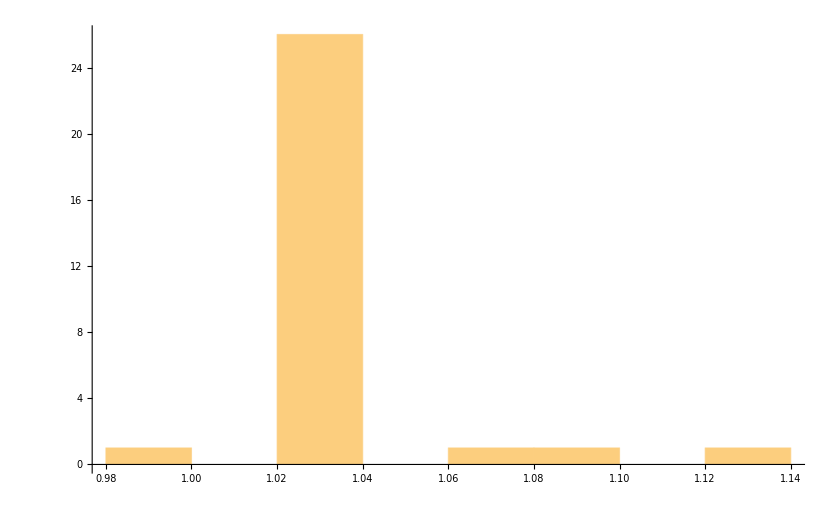

```mathematica
results={};
fitDim=5;
rMax=25;
nGrd=100;
nIter=30;
Do[
linCoeffMin=RandomReal[{0,1}];
linCoeffMax=RandomReal[{100,10000}];
nonlinCoeffMin=RandomReal[{0,0.2}];
nonlinCoeffMax=RandomReal[{40,50}];
tmpCore=FitCoreToGauss[fitDim,JacobiTrailWavefunctionDataF,linCoeffMin,linCoeffMax,nonlinCoeffMin,nonlinCoeffMax];

tmp=GetERE[2,rMax,nGrd,tmpCore];

AppendTo[results,tmp[[1]]];
Print["Heureka! a_(trimer - trimer) = ",results[[-1]],tmpCore]
,{nn,Range[nIter]}]
Histogram[results,{0.02}]
```